```mathematica
<<Units`
```

```mathematica
<<PhysicalConstants`
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
dσdΩ=α^2/me^2 P^2/2(P+1/P-Sin[θ]^2)/.P->1/(1+k/me(1-Cos[θ]));
```

```mathematica
dσdθ=(α^2 (1+1/(1+(k (1-Cos[θ]))/me)+(k (1-Cos[θ]))/me-Sin[θ]^2))/(2 me^2 (1+(k (1-Cos[θ]))/me)^2)*2Pi*Sin[θ];
```

```mathematica
f[θ_]:=k(1-1/(1+k/me(1-Cos[θ])))
```

```mathematica
test=Integrate[dσdθ*f[θ],θ];
```

```mathematica
test1=test/.θ->Pi;
```

```mathematica
test2=test/.θ->0;
```

```mathematica
test1-test2//Simplify
```

1/(3 k^2 me (2 k+me)^3)π α^2 (2 k (-10 k^4+51 k^3 me+93 k^2 me^2+51 k me^3+9 me^4)+3 (2 k+me)^3 (k^2-2 k me-3 me^2) Log[-2 k-me]-3 (2 k+me)^3 (k^2-2 k me-3 me^2) Log[-me])

```mathematica
sptest=1/(3 k^2 me (2 k+me)^3)π α^2 (2 k (-10 k^4+51 k^3 me+93 k^2 me^2+51 k me^3+9 me^4)+3 (2 k+me)^3 (k^2-2 k me-3 me^2) Log[-2 k-me]-3 (2 k+me)^3 (k^2-2 k me-3 me^2) Log[-me]);
```

```mathematica
testcompton=LogLogPlot[sptest(5.*^5)/.{me->0.5,α->1/137},{k,1,10^10},PlotStyle->Dashed];
```

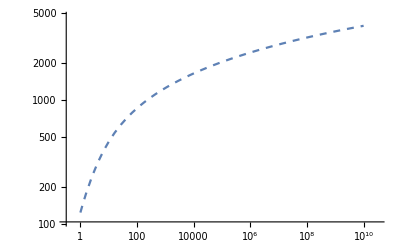

```mathematica
testcompton
```

#### With Pauli-Blocking:

```mathematica
ff[x_]:=f[θ]/.Cos[θ]->x
```

```mathematica
dσdx=(α^2 (1+1/(1+(k (1-x))/me)+(k (1-x))/me-(1-x^2)))/(2 me^2 (1+(k (1-x))/me)^2)*2Pi;
```

```mathematica
ff[x]/Ef
```

(k (1-1/(1+(k (1-x))/me)))/Ef

```mathematica
npiecewise:=Piecewise[{{n ff[x]/Ef,x>1+(Ef me)/((Ef-k) k)},{n,x≤1+(Ef me)/((Ef-k) k)}}]
```

```mathematica
ReplaceAll[dσdx*ff[x]*npiecewise/.{me->0.5,α->1/137,Ef->(3 Pi^2 n)^(1/3)},n->8]
```

1/(1+2. k (1-x))^2 0.000669528 k (1-1/(1+2. k (1-x))) (1/(1+2. k (1-x))+2. k (1-x)+x^2) (Piecewise[{{(4 k (1-1/(1+2. k (1-x))))/(3^(1/3) π^(2/3)), x>1+3.09367/(k (-k+2 3^(1/3) π^(2/3)))}, {8, x≤1+3.09367/(k (-k+2 3^(1/3) π^(2/3)))}, {0, True}}])

```mathematica
ReplaceAll[dσdx*ff[x]*n/.{me->0.5,α->1/137,Ef->(3 Pi^2 n)^(1/3)},n->8]
```

(0.00535622 k (1-1/(1+2. k (1-x))) (1/(1+2. k (1-x))+2. k (1-x)+x^2))/(1+2. k (1-x))^2

```mathematica
Manipulate[Plot[{1/(1+2. k (1-x))^2 0.0006695279777483708 k (1-1/(1+2. k (1-x))) (1/(1+2. k (1-x))+2. k (1-x)+x^2) (Piecewise[{{(4 k (1-1/(1+2. k (1-x))))/(3^(1/3) π^(2/3)), x>1+3.0936677262801355/(k (-k+2 3^(1/3) π^(2/3)))}, {8, x≤1+3.0936677262801355/(k (-k+2 3^(1/3) π^(2/3)))}, {0, True}}]),(0.005356223821986967 k (1-1/(1+2. k (1-x))) (1/(1+2. k (1-x))+2. k (1-x)+x^2))/(1+2. k (1-x))^2},{x,-0.99,0.99}],{k,7,12}]
```

```mathematica
testpauli=Integrate[dσdx*ff[x]*n ff[x]/Ef,x];
```

```mathematica
Solve[ff[x]==Ef,x]//FullSimplify
```

{{x→1+(Ef me)/((Ef-k) k)}}

```mathematica
testpauli1=testpauli/.x->1+(Ef me)/((Ef-k) k);
```

```mathematica
testpauli2=testpauli/.x->1;
```

```mathematica
testpaulinon=Integrate[dσdx*ff[x]n,x];
```

```mathematica
testpaulinon1=testpaulinon/.x->-1;
```

```mathematica
testpaulinon2=testpaulinon/.x->1+(Ef me)/((Ef-k) k);
```

```mathematica
spcomp=(testpauli1-testpauli2)+(testpaulinon1-testpaulinon2)//Simplify;
```

```mathematica
compton=LogLogPlot[ReplaceAll[-spcomp(5.*^5)/.{me->0.5,α->1/137,Ef->(3 Pi^2 n)^(1/3)},{n->8}],{k,1,10^8},PlotStyle->Green];
```

```mathematica
Ef->(3 Pi^2 n)^(1/3)/.n->8//N
```

Ef→6.18734

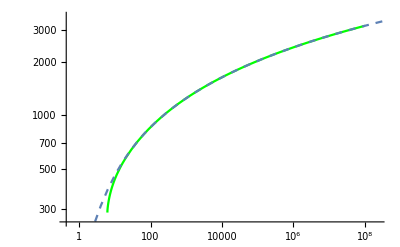

```mathematica
Show[compton,testcompton]
```

#### Full Klein-Nishina scattering cross section (averaged over scattering angles) - k=ω/m_e

```mathematica
σ=2Pi α^2/me^2((1+k)/k^2((2(1+k))/(1+2k)-Log[1+2k]/k)+Log[1+2k]/(2k)-(1+3k)/(1+2k)^2);
```

#### Two limits:

```mathematica
Normal[Series[σ,{k,0,0}]]
```

(8 π α^2)/(3 me^2)

```mathematica
FullSimplify[Normal[Series[σ/.k->1/x,{x,0,1}]]/.x->me/ω]
```

(π α^2 (1+Log[4]-2 Log[me/ω]))/(2 me ω)

#### EM shower E_crit σ_compton= σ_pp

```mathematica
4 α^3/me^2 Z^2Log[10]*Sqrt[0.1/k]/.{me->0.511,α->1/137,Z->1}
```

4.33783×10^-6 √(1/k)

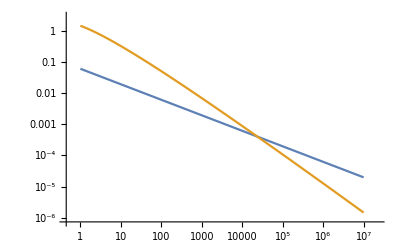

```mathematica
LogLogPlot[{4.3378265073410035*^-6 √(1/k)*6^2*400,(0.0001673819944370927 (1+Log[16. k^2]))/k 6*400},{k,1,10000000}]
```